# Boltzmann Machines

### Create random machine

```mathematica
W=RandomReal[{-100,+100},{8,8}];
Do[W[[i,i]] = 0,{i,8}];
W=W+Wᵀ;
theta=RandomReal[10,8]
```

{1.61774,1.59199,6.23438,9.12609,0.385318,5.11184,4.29862,2.30346}

### Fundamental algorithm

```mathematica
Energy[w_,θ_][s_] := θ . s - ((s . w. s)/2);
```

```mathematica
UpdateState[w_,θ_][s_]:= With[{s2 = MapAt[1-#&, s, RandomInteger[{1,Length[s]}]]},
If[Energy[w,θ][s2]<Energy[w,θ][s],s2,s]]
```

### Utility functions

```mathematica
graycode[n_]:=Map[IntegerDigits[#,2,n]&,Map[BitXor[#,Floor[#/2]]&,Range[0,2^n-1]]]
```

```mathematica
Converge[w_,θ_][state_]:=Nest[UpdateState[w,θ],state,300]
```

```mathematica
FindAttractors[w_,θ_][state_] := Tally[Table[Converge[w,θ][state],{i,40}]]
```

```mathematica
FindBasins[w_,θ_]:={ FindAttractors[w,θ][#],#}&/@graycode[Length[θ]]
```

#### Basins Of Attraction

```mathematica
basins = FindBasins[W, theta];
```

### The Attractors

```mathematica
nbrs[state_]:=Table[ReplacePart[state,i->1-state[[i]]],{i,Length[state]}]
MinimumQ[w_,θ_][state_]:=Min[Map[Energy[w,θ],nbrs[state]]] > Energy[w,θ][state];
AllAttractors[w_,θ_]:= Select[Tuples[{0,1},Length[θ]], MinimumQ[w,θ]];
```

```mathematica
att1=AllAttractors[W,theta];
att=Cases[graycode[8],Alternatives@@att1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1},{0,1,1,0,0,0,0,0},{1,0,1,0,0,1,0,1},{1,0,0,0,0,1,1,1}}

### Colouring Scheme for the Hilbert Curve

```mathematica
blend[{x_}, {_}] := x;
blend[a_, b_]:=Blend[a,b]; 
colourmap[l_]:= Hue[(Flatten[Position[att,l]]-1.0)/(Length[att])]
weightedcolour[l_] := blend[Map[colourmap, l[[All,1]]], l[[All,2]]];
```

```mathematica
colourmap /@ att
```

{Hue[{0.}],Hue[{0.2}],Hue[{0.4}],Hue[{0.6000000000000001}],Hue[{0.8}]}

#### Indexing

```mathematica
Indexpos[k_][{a_,b_}]:={a,k}
PutIndex[lis_]:=Module[{l={}},For [p=1,p<=Length[lis],p++,AppendTo[l,Indexpos[p][lis[[p]]]]];l]
```

### Hilbert Curve : 1-D =>> 2-D map

```mathematica
rot[s_,x_,y_,rx_,ry_]:=Module[ {x1=x,y1=y,tp},

If[ry==0,If[rx==1,x1=s-1-x;y1=s-1-y;];tp=x1;x1=y1;y1=tp;];
{s,x1,y1,rx,ry}
]
d2xy[n_][d_]:=Module[{rx,ry,t=d,x=0,y=0,s},
For[s=1,s<n,s*=2,rx=BitAnd[1,Floor[(t/2)]];ry=BitAnd[1,BitXor[t,rx]];
{s,x,y,rx,ry}=rot[s,x,y,rx,ry];x=x+(s*rx);y=y+(s*ry);t=Floor[t/4];
];
{x,y}
]
```

## Execution:

```mathematica
MapHilbert[l_,n_]:= MapThread[{#1,d2xy[n][#2]}&,Transpose@l]
h={weightedcolour[#1], #2}& @@@ MapHilbert[PutIndex[basins],16];
```

```mathematica
arr=ConstantArray[0,{16,16}];
setarr[col_, {p1_,p2_}]:=arr[[1+p1,1+p2]]=col;
setarr @@@ h;
```

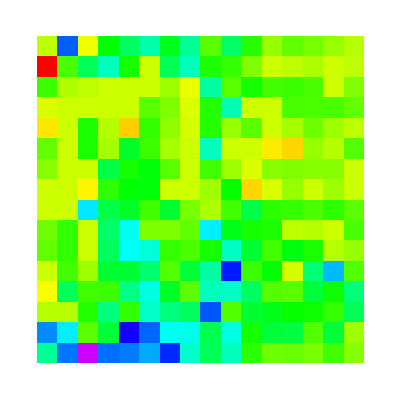

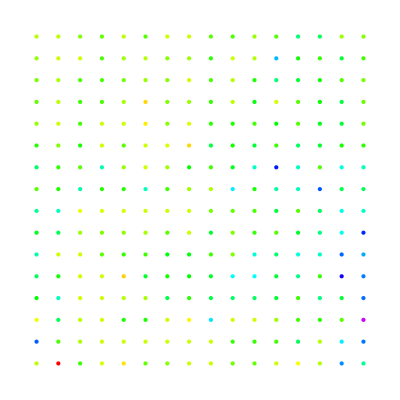

```mathematica
ArrayPlot[arr]

Graphics[{PointSize[Large],Style[Point[#2],#1]&@@@h}]
```